```mathematica
(*Define the functions*)
ξ[r_,a_,M_]:=(a^2 M+a^2 r-3 M r^2+r^3)/(a (M-r));

η[r_,a_,M_]:=-(r^3 (-4 a^2 M+9 M^2 r-6 M r^2+r^3))/(a^2 (M-r)^2);

α[r_,a_,M_,theta_]:=(-ξ[r,a,M])/Sin[theta];

β[r_,a_,M_,θ_]:=√(η[r,a,M]+a^2 Cos[θ]^2-ξ[r,a,M]^2 Cot[θ]^2);
```

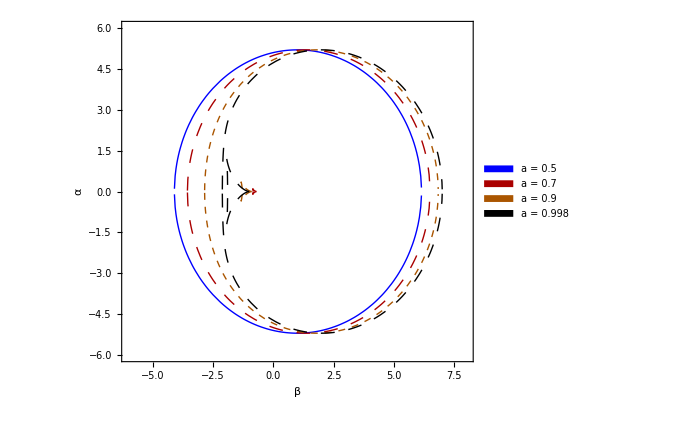

```mathematica
(*Create the parametric plot with an integrated legend*)
ParametricPlot[{{α[r,0.5,1,π/2],β[r,0.5,1,π/2]},{α[r,0.5,1,π/2],-β[r,0.5,1,π/2]},{α[r,0.7,1,π/2],β[r,0.7,1,π/2]},{α[r,0.7,1,π/2],-β[r,0.7,1,π/2]},{α[r,0.9,1,π/2],β[r,0.9,1,π/2]},{α[r,0.9,1,π/2],-β[r,0.9,1,π/2]},{α[r,0.998,1,π/2],β[r,0.998,1,π/2]},{α[r,0.998,1,π/2],-β[r,0.998,1,π/2]}},{r,-8,8},PlotStyle->{{Blue,Thick},{Blue,Thick},{Darker[Red],Dashing[{0.02,0.02}],Thick},{Darker[Red],Dashing[{0.02,0.02}],Thick},{Darker[Orange],Dashed,Thick},{Darker[Orange],Dashed,Thick},{Black,Dashing[{0.02,0.02}],Thick},{Black,Dashing[{0.02,0.02}],Thick}},PlotRange->{{-6,8},{-6,6}},Frame->True,Axes->True,FrameLabel->{"β","α"},FrameStyle->Directive[Black,16],ImageSize->500,PlotLegends->Placed[SwatchLegend[{Blue,Darker[Red],Darker[Orange],Black},{"a = 0.5","a = 0.7","a = 0.9","a = 0.998"},LegendMarkerSize->20],{Left,Bottom}]]
```